```mathematica
{FullForm[a*b+c],FullForm[a+b*c]}(*tells orders of operation, precedence*)
```

{Plus[Times[a,b],c],Plus[a,Times[b,c]]}

```mathematica
(*plus is a flat function, / left grouping and ^ is right grouping eg*)
FullForm[x+y+z]
FullForm[x/y/z]
FullForm[x^y^z]
```

Plus[x,y,z]

Times[x,Power[y,-1],Power[z,-1]]

Power[x,Power[y,z]]

```mathematica
∫k[x]ⅆx // FullForm
```

Integrate[k[x],x]

```mathematica
∫(a[x]+b[x])ⅆx  (*requires parantheses inside due to low priority of + function, times is okay though*)
```

∫(a[x]+b[x])ⅆx

```mathematica
x^(a+b) (*superscript is power)
```

```mathematica
∂_x x^n (*partial derivative operator*)
```

n x^(-1+n)

```mathematica
∑_(n=1)^∞ 1/n^s + n  (*Summinzg has higher precedence than +*)
```

```mathematica
n+Zeta[s]
```

n+Zeta[s]

```mathematica
(*() are for grouping*)
(*[] are for functions*)
(*{} are for lists*)
(* v[[i]] double brackets for indexing*)
```

```mathematica
(*examples*)
{1,2,3,4,5}
v =Range[10]
Sin[2]
v
v[[3]]
```

{1,2,3,4,5}

{1,2,3,4,5,6,7,8,9,10}

Sin[2]

{1,2,3,4,5,6,7,8,9,10}

3

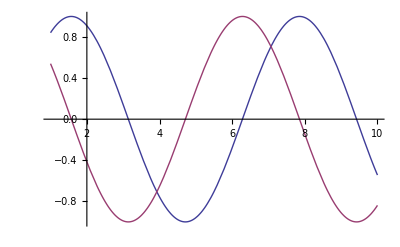

```mathematica
Plot[{Sin[x],Cos[x]},{x,1,10}]
```

```mathematica
(*symbolic computation is tight, this kid does algebra and stuff for you*)
3x^2-x^2+1
```

1+2 x^2

```mathematica
(*the function expand will multiply out products and powers, the factor function will do the inverse*)
Expand[(3(x+y)^2)]
```

3 x^2+6 x y+3 y^2

```mathematica
(*to assign a value to a variable use the transformation rule*)
1+2 x/.x->3
```

7

```mathematica
(*you could also replace x with another expression*)
1 + 2x /. x->y+2
```

1+2 (2+y)

```mathematica
(*The functions Simplify and FullSimplify will simplify any expression as much as possible*)
Simplify[x^2+2x+1]
```

(1+x)^2

```mathematica
Simplify[Gamma[x]Gamma[1-x]]
FullSimplify[Gamma[x]Gamma[1-x]]
```

Gamma[1-x] Gamma[x]

π Csc[π x]

```mathematica
(*Now for derivatives! D[f,x] is partial with respect to x
D[f,x,y,...] will apply multiple derivative operators
D[f,{x,n}]  gives the nth partial derivative
D[f,x,NonConstants->{v1,v2,...}] i don't realy understand this. Ask Dr. Klay or Gutierrez*)

D[x^2+y^2,x]
```

2 x

```mathematica
(*now for integrals*)
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
Integrate[x^x,x]
```

∫x^x ⅆx

```mathematica
(*for definite integrals*)
Integrate[Sin[x]^2,{x,a,b}]
```

1/2 (-a+b+Cos[a] Sin[a]-Cos[b] Sin[b])

```mathematica
Integrate[x^x,{x,0,1}]
```

∫_0^1 x^x ⅆx

```mathematica
Integrate[x^2,x]
```

x^3/3

```mathematica
Integrate[1/(x^2-1),x]
```

```mathematica
1/2 Log[1-x]-1/2 Log[1+x]
D[%.x]
```

1/2 Log[1-x]-1/2 Log[1+x]

(1/2 Log[1-x]-1/2 Log[1+x]).x

```mathematica
Simplify[%]
```

```mathematica
(1/2 (Log[1-x]-Log[1+x])).x
FullSimplify[%]
```

(1/2 (Log[1-x]-Log[1+x])).x

(-ArcTanh[x]).x

```mathematica
(*DSolve solves all the DE's brah*)
DSolve[y'[x]+y[x]==1,y[x],x]
```

{{y[x]→1+ⅇ^-x C[1]}}

```mathematica
DSolve[y'[x]+y[x]==1,y,x]
```

{{y→Function[{x},1+ⅇ^-x C[1]]}}

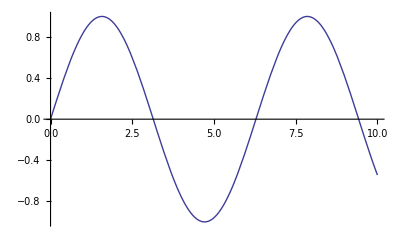

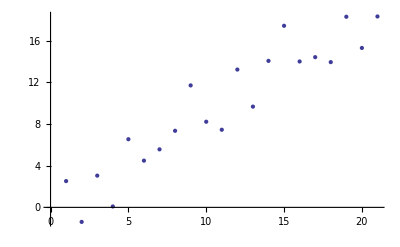

```mathematica
(*DSolve[{eqn1,eqn2,...},{y1,y2,...},x]*)
(*^solves lists of diff eq's*)

(*Plot plots a function whereas ListPlot plots data points*)
Plot[Sin[x],{x,0,10}]
datapts=Table[x+RandomReal[{-4,4}],{x,0,20}];
ListPlot[datapts]
```

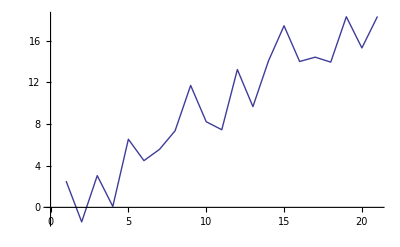

-Graphics3D-

```mathematica
(*you can also connect the points wit ListLinePlot*)
ListLinePlot[datapts]
(*and Plot3D will plot in 3d*)
Plot3D[Sin[x]Cos[y],{x,0,5},{y,1,10}]
```

```mathematica
(*you can customize like in python*)
{{(*GraphicsGrid[{{Plot3D[Sin[x] Cos[y],{x,0,5},{y,1,10}],Plot3D[Sin[x]*Cos[y],{x,0,5},{y,1,10},ColorFunction->(Hue[#3]&),MeshFunctions->(#3&),Boxed->False,Axes->False]}}]}, {□}}
```

```mathematica
(*different types of 1d plots*)
```

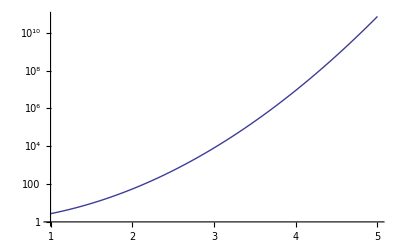

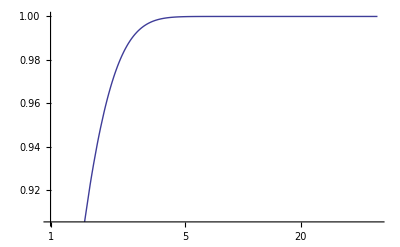

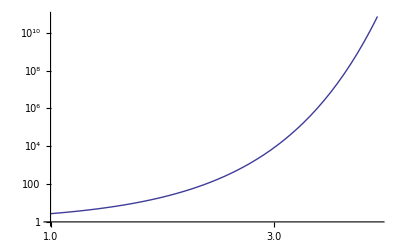

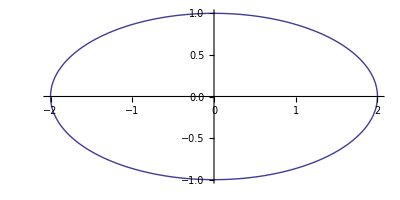

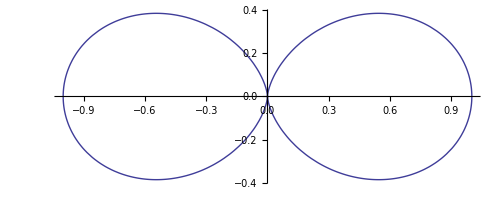

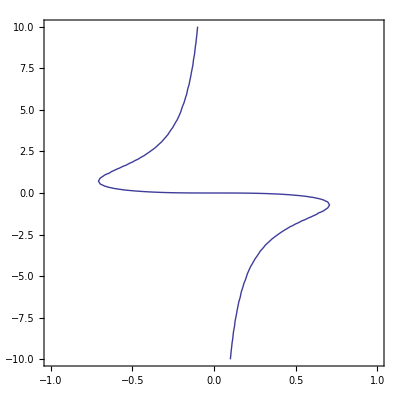

```mathematica
LogPlot[E^x^2,{x,1,5}]
LogLinearPlot[Tanh[x],{x,1,50}]
LogLogPlot[E^x^2,{x,1,5}]
ParametricPlot[{2 Sin[t],Cos[t]},{t,0,2 Pi}]
PolarPlot[Cos[t]^2,{t,0,2 Pi}]
ContourPlot[x^3+x y^2+y==0,{x,-1,1},{y,-10,10}]
```

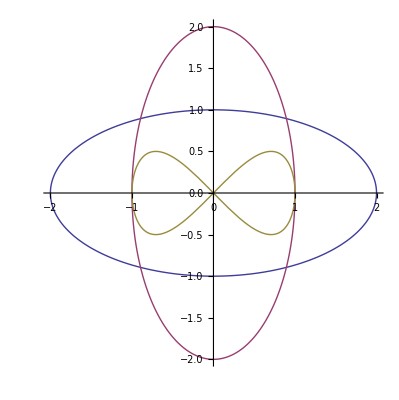

```mathematica
(*Muli-parametric plots*)
ParametricPlot[{{2 Sin[t],Cos[t]},{Sin[t],2 Cos[t]},{Sin[t],Sin[t] Cos[t]}},{t,0,2 Pi}]
```

```mathematica
ParametricPlot3D[{5 Cos[u],5 Sin[u],u+Sin[u]},{u,-2 Pi,2 Pi}]
```

-Graphics3D-

{{y→InterpolatingFunction[{{-10.,10.}},<>]}}

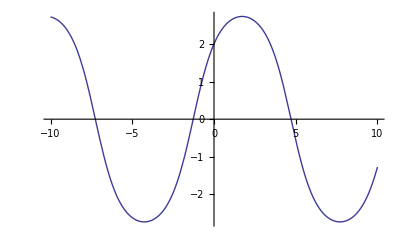

```mathematica
ode1={y''[x]+Sin[y[x]]==0,y[0]==2,y'[0]==1};
sol=NDSolve[ode1,y,{x,-10,10}]
Plot[y[x]/.sol,{x,-10,10}]
```

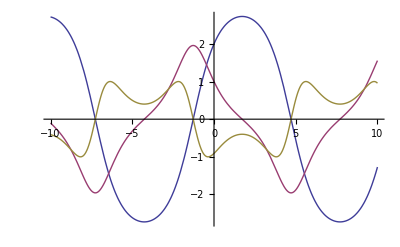

```mathematica
(*plotting with the derivatives too!*)
Plot[Evaluate[{y[x],y'[x],y''[x]}/.sol],{x,-10,10}]
```

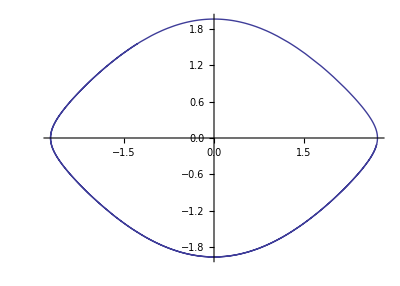

```mathematica
(*I don't really understand what this is plotting either*)
ParametricPlot[Evaluate[{y[x],y'[x]}/.sol],{x,-10,10}]
```

```mathematica
(*lets you vary initial conditions*)
Manipulate[Module[{sol=NDSolve[{y''[x]+Sin[y[x]]==0,y[0]==p[[1]],y'[0]==p[[2]]},y,{x,0,T}]},ParametricPlot[Evaluate[{y[x],y'[x]}/.sol],{x,0,T},PlotRange->{{-4,4},{-3,3}}]],{{p,{2,1}},Locator},{{T,10},0,100}]
```

```mathematica
(*you can have a plot animate with time*)
wws = NDSolve[{D[u[t,x], t,t] == D[u[t,x], x,x] + (1 - u[t, x]^2) (1 + 2 u[t, x]), u[0, x] == E^-x^2, 
Derivative[1,0][u][0, x] == 0, u[t, -10] == u[t, 10]}, 
  u, {t, 0, 10}, {x, -10, 10}];
plots=Table[Plot[u[t,x]/.wws,{x,-10,10},PlotRange->{-2,2}],{t,0,10,.25}];
ListAnimate[plots]
```

```mathematica
(*LEARNING THE MANIPULATE FUNCTIONS :D*)
Table[n,{n,1,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Manipulate[n,{n,1,20}]
```

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,20}]
```

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,20,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},PlotRange->2],{n1,1,20},{n2,1,20}]
```

```mathematica
Manipulate[Expand[(α+β)^n],{n,1,20}]
```

```mathematica
(*With and explicit step function*)
Manipulate[n,{n,1,20,1}]
```

```mathematica
Manipulate[Expand[(α+β)^n],{n,1,20,1}]
```

```mathematica
Manipulate[Row[{n,"+",m,"=",n+m}],{n,1/2,1/3,1/144},{m,1/2,1/3,1/144}]
```

```mathematica
Manipulate[Row[{n,"+",m,"=",n+m}],{n,a,10 a,a/12},{m,a,10 a,a/12}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom}}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Frame->frame,PlotRange->2],{n1,1,20},{n2,1,20},{frame,{True,False}}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom,Automatic,2,1,0,-1,-2},ControlType->SetterBar}]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{n1,1,4},{a1,0,1},{p1,0,2 Pi},{n2,1,4},{a2,0,1},{p2,0,2 Pi}]
```

```mathematica
(* you can also add labels to the nonsense*)
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{{n1,1,"Frequency 1"},1,4},{{a1,1,"Amplitude 1"},0,1},{{p1,0,"Phase 1"},0,2 Pi},{{n2,5/4,"Frequency 2"},1,4},{{a2,1,"Amplitude 2"},0,1},{{p2,0,"Phase 2"},0,2 Pi}]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{{n1,1,"Frequency 1"},1,4},{{a1,1,"Amplitude 1"},0,1},{{p1,0,"Phase 1"},0,2 Pi},{{n2,5/4,"Frequency 2"},1,4},{{a2,1,"Amplitude 2"},0,1},{{p2,0,"Phase 2"},0,2 Pi},ControlPlacement->Left]
```

```mathematica
(*all beauty syntax standards can be found here :)*)
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],Style["Horizontal",12,Bold],{{n1,1,"Frequency"},1,4},{{a1,1,"Amplitude"},0,1},{{p1,0,"Phase"},0,2 Pi},Delimiter,Style["Vertical",12,Bold],{{n2,5/4,"Frequency"},1,4},{{a2,1,"Amplitude"},0,1},{{p2,0,"Phase"},0,2 Pi},ControlPlacement->Left]
```